## TT[] is the dispersion relation function, a is lattice constant, and kx,ky are momentum.

```mathematica
TT[kx_,ky_,a_]:=-2(Cos[kx a]+Cos[(kx a /2)+(ky a Sqrt[3]/2)]+Cos[kx a /2-(ky a Sqrt[3]/2)]);
```

### plot the dispersion relation in 3D way.

```mathematica
Plot3D[TT[x,y,1],{x,-4Pi/3,4Pi/3},{y,-2Pi/Sqrt[3],2Pi/Sqrt[3]},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤4Pi/3&&Abs[x-y/Sqrt[3]]≤4Pi/3],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

#### Plot dispersion relation in contourplot way.

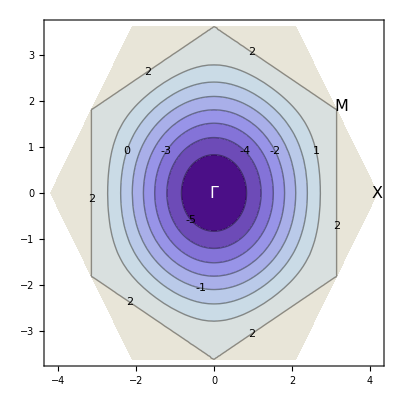

```mathematica
ContourPlot[TT[x,y,1],{x,-4Pi/3,4Pi/3},{y,-2Pi/Sqrt[3],2Pi/Sqrt[3]},RegionFunction->Function[{x,y},Abs[x+y/Sqrt[3]]≤4Pi/3&&Abs[x-y/Sqrt[3]]≤4Pi/3],Epilog->{White,Text[Style[Γ,16],{0,0}],Black,Text[Style[M,16],{Pi+0.12,(Pi+0.12)/Sqrt[3]}],Black,Text[Style[X,16],{4Pi/3,0}]},ContourLabels->All]
```

#### Plot dispersion relation along Γ----M-----X----Γ path.

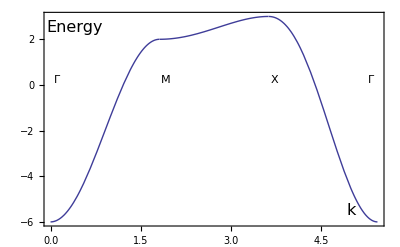

```mathematica
Plot[Piecewise[{{TT[Sqrt[3]t,t,1],t≥0&&t<Pi/Sqrt[3]},{TT[(t-Pi/Sqrt[3])/Sqrt[3]+Pi,(2Pi/Sqrt[3]-t),1],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{TT[4/Sqrt[3](Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,1],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

#### ARPES Measurement AA[] is the spectral density function

```mathematica
AA[kx_,ky_,e_,δ_]:=δ/Pi/((e-TT[kx,ky,1])^2+δ^2)
```

#### Choose δ=0.7 and plot AA[]

```mathematica
DensityPlot[Piecewise[{{AA[Sqrt[3]t,t,z,0.7],t≥0&&t<=Pi/Sqrt[3]},{AA[(t-Pi/Sqrt[3])/Sqrt[3]+Pi,(2Pi/Sqrt[3]-t),z,0.7],t≥Pi/Sqrt[3]&&t<=2Pi/Sqrt[3]},{AA[4/Sqrt[3](Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,z,0.7],t≥2Pi/Sqrt[3]&&t<=3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},{z,-6,3},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

-Graphics-

#### MDC, kx=ky*Sqrt[3]={π/6,π/6+0.4,π/6+0.8,π/6+1.2,π/6+1.6,}

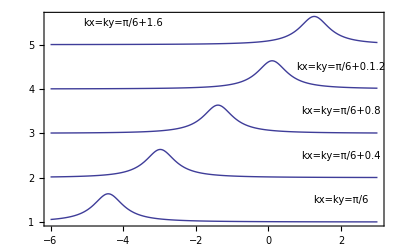

```mathematica
Plot[Table[AA[Pi/6+0.4i,(Pi/6+0.4i)/Sqrt[3],e,0.5]+i,{i,5}],{e,-6,3},PlotRange->Full,Epilog->{Inset[Style["kx=ky=π/6",10],{2,1.5}],Inset[Style["kx=ky=π/6+0.4",10],{2,2.5}],Inset[Style["kx=ky=π/6+0.8",10],{2,3.5}],Inset[Style["kx=ky=π/6+0.1.2",10],{2,4.5}],Inset[Style["kx=ky=π/6+1.6",10],{-4,5.5}]},Frame->True]
```

#### EDC, E={-5,-3,-1,1,3}

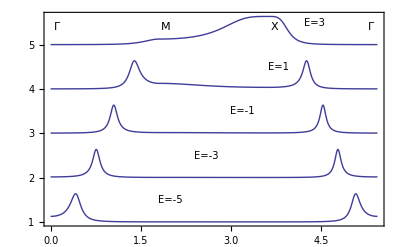

```mathematica
Plot[Table[Piecewise[{{AA[Sqrt[3]t,t,2z-7,0.5],t≥0&&t<Pi/Sqrt[3]},{AA[(t-Pi/Sqrt[3])/Sqrt[3]+Pi,(2Pi/Sqrt[3]-t),2z-7,0.5],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{AA[4/Sqrt[3](Pi/Sqrt[3]-(t-2Pi/Sqrt[3])),0,2z-7,0.5],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}]+z,{z,5}],{t,0,Sqrt[3]Pi},PlotRange->Full,Epilog->{Inset[Style["E=-5",10],{2,1.5}],Inset[Style["E=-3",10],{2.6,2.5}],Inset[Style["E=-1",10],{3.2,3.5}],Inset[Style["E=1",10],{3.8,4.5}],Inset[Style["E=3",10],{4.4,5.5}],Inset["Γ",{0.1,5.4}],Inset["M",{Pi/Sqrt[3]+0.1,5.4}],Inset["X",{2Pi/Sqrt[3]+0.1,5.4}],Inset["Γ",{3Pi/Sqrt[3]-0.1,5.4}]},Frame->True,GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}}]
```

#### DRAC is the drac function in lorenz form with small parameter δ. and Dos is the density of state function with varying energy.

```mathematica
DRAC[t_,δ_]:=δ/Pi/(t^2+δ^2);
Dos[e_]:=NIntegrate[Boole[Abs[x+y/Sqrt[3]]≤4Pi/3&&Abs[x-y/Sqrt[3]]≤4Pi/3]DRAC[e-TT[x,y,1],0.1],{x,-4Pi/3,4Pi/3},{y,-2Pi/Sqrt[3],2Pi/Sqrt[3]}]
```

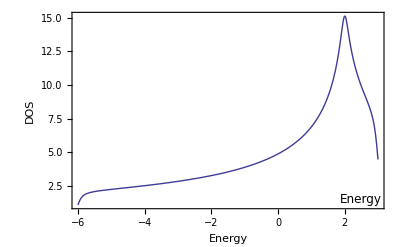

```mathematica
Plot[Dos[z],{z,-6,3},Frame->True,AxesLabel->{Energy,DOS},Epilog->{Inset[Style["Energy",12],{2.5,1.5}]}]
```

```mathematica
Array[EN,200];
```

```mathematica
nn=1;While[nn<201,EN[nn]=0;nn++];
```

```mathematica
EN[200]
```

0

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=TT[i Pi/100-Pi,2j Pi/Sqrt[3]/100-2Pi/Sqrt[3],1]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy,{-6,3},{0,200}]//Round;    (* find appropriate bin *)
EN[n]++
}
]
]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

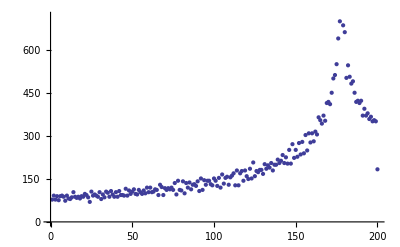

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,200}]]
```

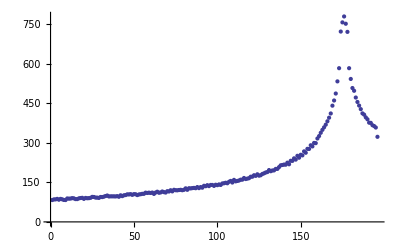

```mathematica
ListPlot[Table[{i,(EN[i]+EN[i+1]+EN[i+2]+EN[i+3]+EN[i+4])/5},{i,0,200}]]
```